This file is the data processing for the backscattering simulations. A count is kept of how many events backscattered, and a histogram for the energies of the backscattered electrons is produced. The percentage of electrons that backscattered is calculated. The imported file can be swapped to see backscattering for polystyrene rather than CsI.

```mathematica
SetDirectory[NotebookDirectory[]];
data = Import["CesiumIodideData.txt","Data"];
```

```mathematica
data = Flatten[data];
dataE={};
nBackScatter =0;
len=Length[data];
For[i=1,i≤Length[data],++i,
If[data[[i]]>0,nBackScatter = nBackScatter + 1];
If[data[[i]]>0,AppendTo[dataE,data[[i]]]]
]
```

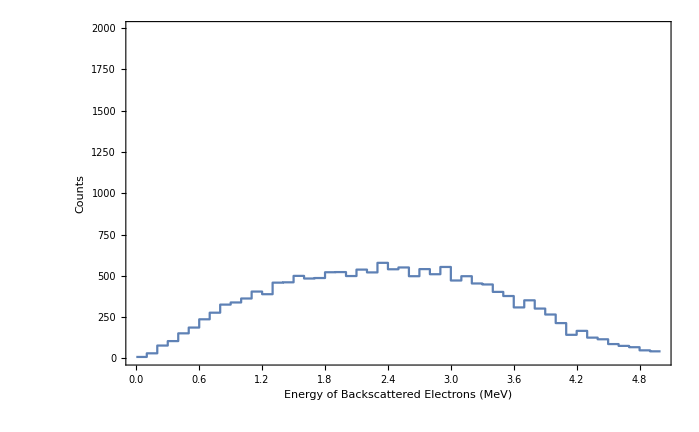

16636

2.38635

1.05062

```mathematica
hist=HistogramList[dataE,{.1}];

ListPlot[Transpose[{hist[[1]],ArrayPad[hist[[2]],{0,1},"Fixed"]}],InterpolationOrder->0,Joined->True,AxesOrigin->{0,0},PlotRange->{{0,5},{0,2000}},RotateLabel->True,FrameLabel->{Style["Energy of Backscattered Electrons (MeV)",20,Bold,Blue],Style["Counts",20,Bold,Blue]},
LabelStyle->Directive[Blue,Bold],Frame->True]
Length[dataE]
Mean[dataE]
StandardDeviation[dataE]
```

```mathematica
percentBackScatter=100*N[nBackScatter/len]
```

16.636